```mathematica
(* http://www.powerfromthesun.net/Book/chapter02/chapter02.html#ZEqnNum929295 *)

year = 2016;
(* parameters are forced numeric, so findMaximum in dayangle works better *)
angle[i_?NumericQ,a_?NumericQ,d_]:= ( (* params: index of sunPositions table, solar panel angle in degrees, date, returns misalignment with the sun in radians *)
sunPos = sunPositions[[i]]; (* lookup sun position *)

(* remove degree unit, then convert to radians *)
gammaS= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
gammaS = gammaS - Pi;
thetaS= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
gammaP = -22 * Pi/180; (* Solar panels azimuth *)
thetaP = a * Pi/180; (* Solar panels angle with horizontal *)
ArcCos[Cos[gammaP-gammaS] Cos[thetaS] Sin[thetaP]+Cos[thetaP] Sin[thetaS]]
)

(* parameters for clear day *)
directPowerClear[x_?NumericQ,a_?NumericQ,d_]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[x,a,d]; (* solar zenith (misalignment) in radians *)
(* here comes the magik formula from http://www.powerfromthesun.net/Book/chapter02/chapter02.html#ZEqnNum929295 for a clear day *)
n= QuantityMagnitude[Quantity[d - DateObject[{2016,1,1}]]]; (* day of year *)
i= 1367 (1+0.034 Cos[360*n/365.25]);
aZero = 0.4237 - 0.00821 36;
aOne = 0.5055 + 0.00595 6.5^2;
k = 0.2711 + 0.01858 2.5^2;
If[Cos[theta]<0,
0,
i (aZero + aOne E^(-k/Cos[theta])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
] 
)

(* parameters from urban visibility haze model *)
directPower[x_?NumericQ,a_?NumericQ,d_]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[x,a,d]; (* solar zenith (misalignment) in radians *)
(* here comes the magik formula from http://www.powerfromthesun.net/Book/chapter02/chapter02.html#ZEqnNum929295 for a clear day *)
n= QuantityMagnitude[Quantity[d - DateObject[{2016,1,1}]]]; (* day of year *)
i= 1367 (1+0.034 Cos[360*n/365.25]);
aZero = 0.2538 - 0.0063 36;
aOne = 0.7678 + 0.001 6.5^2;
k = 0.249 + 0.081 2.5^2;
If[Cos[theta]<0,
0,
i (aZero + aOne E^(-k/Cos[theta])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
] 
)

(* http://www.solarpaneltilt.com/ *)
(*directPowerWeb[x_?NumericQ,a_?NumericQ,d_]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[x,a,d]; (* solar zenith (misalignment) in radians *)
If[theta>Pi/2,
0,
1.35*(1/1.35)^(Sec[theta])*1000
]
)*)

dayAngle := Function[ (* params: day of month, month, returns optimal angle for this day *)

date = DateObject[{year,#2,#1}];

position = GeoPosition[{51.546545,4.411744}];
sunrise = Sunrise[position,date];
TimeZoneConvert[sunrise,2];
sunriseHour = DateValue[sunrise,"Hour"]+DateValue[sunrise, "Minute"]/60;
sunset = Sunset[position,date];
TimeZoneConvert[sunset,2];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
(* generate sun position table, so angle[] can access it every time *)
sunPositions = Table[
 SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[date,{h/100}]],
{h,sunriseHour*100,sunsetHour*100,10}
];
(* Times 100 so the sum starts closer to the real sunUpHour, and not floors it to an integer when calculating the sum. Otherwise weird jumps in graphs appear when the sunUpHour jumps one hour *)

(* Find for which angle of the solar panels this value is maximal,starting at 50 *)

a/. FindMaximum[
Sum[directPower[h,a,date],{h,1,Length[sunPositions],10}]
,{a,50,0,90}, AccuracyGoal->5][[2]]
]

monthAngle := Function [ (* params: month, returns optimal angle for a specific month by taking the average  *)
(* Count how many days are in this month *)
days = With[{first=DateObject[{year,#1,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]] ;
Sum[dayAngle[x,#1],{x,1,days}]/days
]


(******************************** END OF FUNCTIONS  ********************************)
(*angle[1575,0,DateObject[{2016,12,20}]]*180/Pi*)
(*DiscretePlot3D[angle[h,x,DateObject[{2016,12,20}]]*180/Pi,{h,500,2300,10},{x,0,90,10},ImageSize -> Large, AxesLabel -> {"Hour of day", "Panel angle"}]*)
(*angle[1400,40,DateObject[{2016,7,18}]]*180/Pi
directPower[1400,30,DateObject[{2016,7,18}]]*)
(*directPower[1500,0,DateObject[{2016,7,18}]]
directPower[1500,10,DateObject[{2016,7,18}]]
 DiscretePlot[directPower[x,0,DateObject[{2016,7,18}]],{x,500,2300,10},ImageSize -> Large] 
 DiscretePlot[directPower[x,10,DateObject[{2016,7,18}]],{x,500,2300,10},ImageSize -> Large] 
 sumOverDay[0,DateObject[{2016,7,18}]] 
 sumOverDay[10,DateObject[{2016,7,18}]] *)

(* DiscretePlot[sumOverDay[a,DateObject[{2016,7,18}]],{a,0,90,10}] *)
(* NMinimize[{directPower[1400,x,DateObject[{2016,7,18}]],0≤ x ≤ 90},x] *)
(*DiscretePlot3D[directPower[h,a,DateObject[{2016,7,18}]],{h,500,2300,50},{a,0,90,5}]

FindMaximum[directPower[1400,x,DateObject[{2016,7,18}]],{x,0,0,90}, AccuracyGoal->5] //Timing
directPower[1400,50,DateObject[{2016,7,18}]]*)
(* DiscretePlot[sumOverDay[x,DateObject[{2016,7,18}]],{x,0,90,10}] *)

(*NMaximize[{sumOverDay[x,DateObject[{2016,7,18}]],0≤ x ≤ 90},x] //Timing*) (* took 60 secs, .02 for FindMaximum *)
(*FindMaximum[sumOverDay[x,DateObject[{2016,7,18}]],{x,50,0,90}, AccuracyGoal->5]
sumOverDay[0,DateObject[{2016,7,18}]]*)

(*dayAngle[17,8] *)(* around 1.5-2 secs *)
(* lower than 15 degrees: from 7/5 until 5/8 *)

(*DiscretePlot[dayAngle[15,x],{x,1,12},ImageSize->Large,AxesLabel -> {"Month", "optimal angle at 15th"}] //Timing*)

(***** END OF DEBUG ******)

(* Graph for a day *)
(* date = DateObject[{2016,7,18}];
 AbsoluteTiming[DiscretePlot[sumOverDay[x,date],{x,0,90,10},ImageSize->Large,AxesLabel -> {"Solar panel angle", "Total of sun power, W/m^2"}] ] *)

(* Graph for a month *)
 (* month = 9;
days = With[{first=DateObject[{year,month,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]];
AbsoluteTiming[DiscretePlot[dayAngle[a,month],{a,1,days},ImageSize->Large,AxesLabel -> {"Day", "Optimal angle"}]] *)

(* Graph for this year, month average *)
(* AbsoluteTiming[DiscretePlot[monthAngle[x],{x,1,12},ImageSize->Large,AxesLabel -> {"Month", "Average of optimal angle"}] ] *) (* ten minutes *)

(* Comparison with perpendicular to sun at noon, per month, http://www.gogreensolar.com/pages/solar-panel-tilt-calculator *)
(*greenList = {68,60,52,44,36,28,36,44,52,60,68,76};
list = Table[monthAngle[x],{x,1,12}];
ListPlot[{greenList,list},Filling-> Axis,PlotLegends-> {gogreensolar,calculations},ImageSize->Large,AxesLabel -> {"Month", "Average of optimal angle"}]
*)

(* season values *)

(*monthSum[m_,i_,j_] := ( (* month, begin day, end day *)
Sum[
Quiet[dayAngle[x,m]],
{x,i,j}]
)
(* takes winter of [year] only. dates according to solarpaneltilt.com, summer april 18, autumn august 24, winter oct 7, spring march 5 *)
 summerSum = Quiet[monthSum[4,18,30] + monthSum[5,1,31] + monthSum[6,1,30] + monthSum[7,1,31]+ monthSum[8,1,23]];
summerDays = QuantityMagnitude[Quantity[DateDifference[{year,4,18},{year,8,23}]]]+1;
summerSum/summerDays (* 21 degrees *)

autumnSum = monthSum[8,24,31]+ monthSum[9,1,30] + monthSum[10,1,6];
autumnDays = DayCount[{year,8,24},{year,10,6}]+1;
autumnSum/autumnDays (* 49 degrees *)

 winterSum = Quiet[monthSum[10,7,31] + monthSum[11,1,30] +monthSum[12,1,31] + monthSum[1,1,31] + monthSum[2,1,29] + monthSum[3,1,4]];
winterDays = DayCount[{year,10,7},{year+1,3,4}]+1;
winterSum/winterDays  (* 73 degrees *)

springSum = Quiet[monthSum[3,5,31] + monthSum[4,1,17]];
springDays = DayCount[{year,3,5},{year,4,17}]+1;
springSum/springDays (* 49 degrees *)*)

(* Year average *)
(*(winterSum + summerSum + springSum + autumnSum)/366 (* 49 degrees *)*)
(* standalone *)
(*Sum[
days = With[{first=DateObject[{year,m,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]];
Sum[
Quiet[dayAngle[d,m]]
,{d,1,days}]
,{m,1,12}]/ QuantityMagnitude[Quantity[DateDifference[{year,1,1},{year,12,31}]]]+1 (* 50 degrees *)
*)


(* Full graph of year *)
(*dateByDay=Function[x,DateObject[{2016,1,1}]+Quantity[(x-1),"Days"]];

t = Table[{dateByDay[d],Quiet[dayAngle[DateValue[dateByDay[d],"Day"],DateValue[dateByDay[d],"Month"]]]},{d,1,366}]
DateListPlot[t,AxesLabel -> {"Degrees","2016"}]
*)
```

20.6792

48.7523

73.1696

49.1891

48.7941

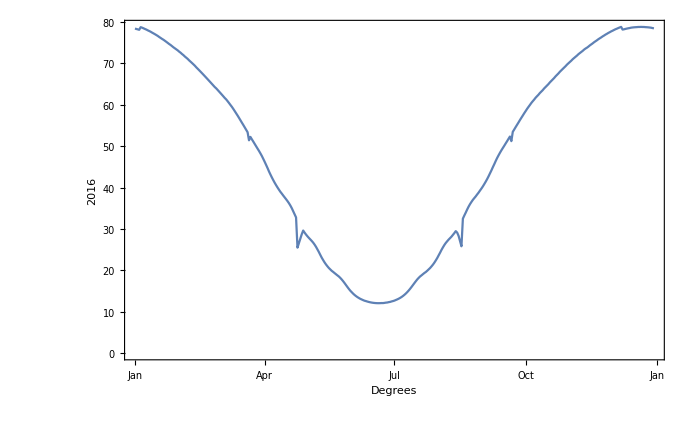
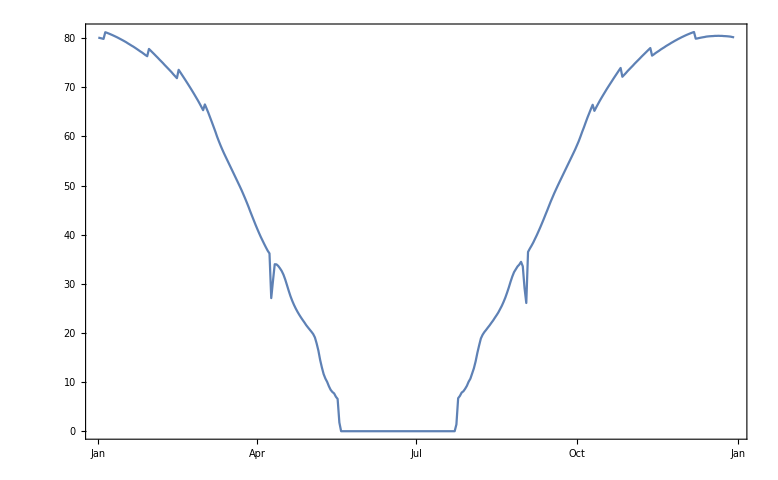
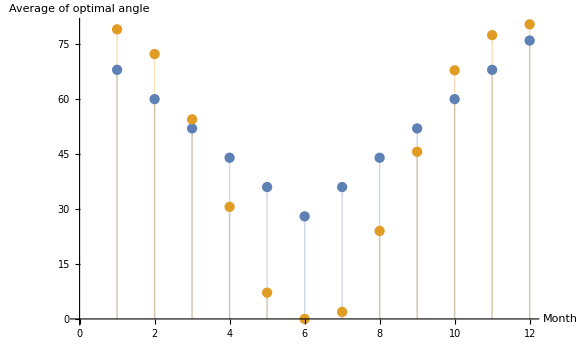
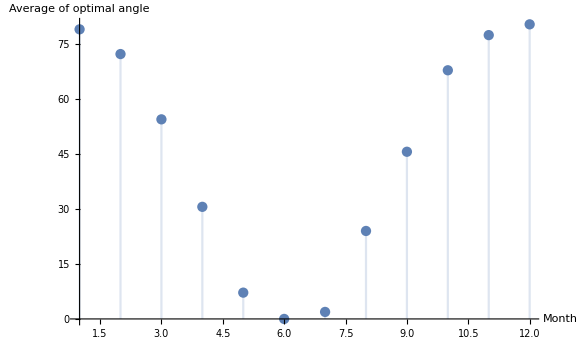
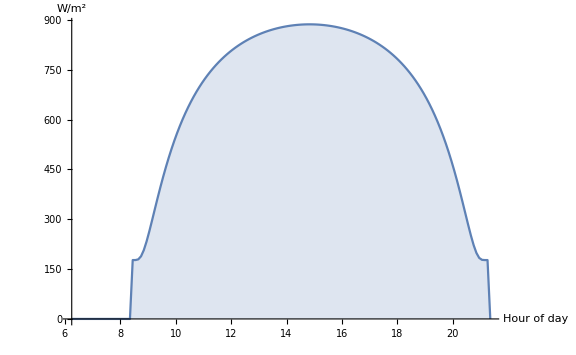
```mathematica
-Graphics-

(******* everything below with clear day parameters *******************)

full graph of year: -Graphics-
comparison gogreensolar -Graphics-
2016:-Graphics-
8/6,30 panel angle-Graphics-
```

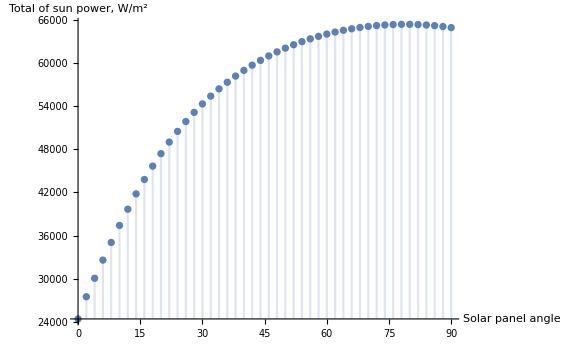
```mathematica
december first:-Graphics-
```

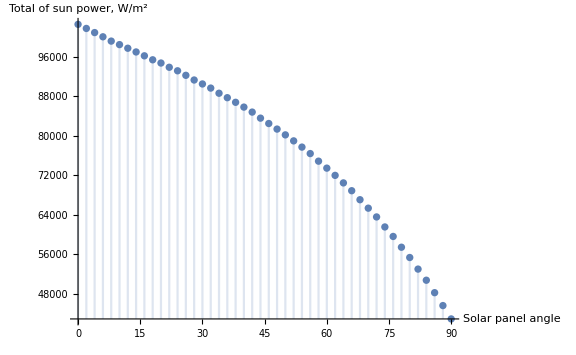
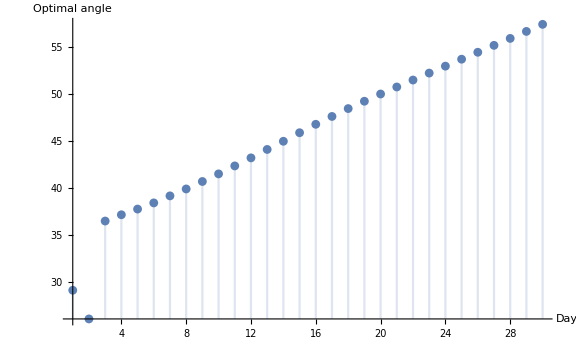
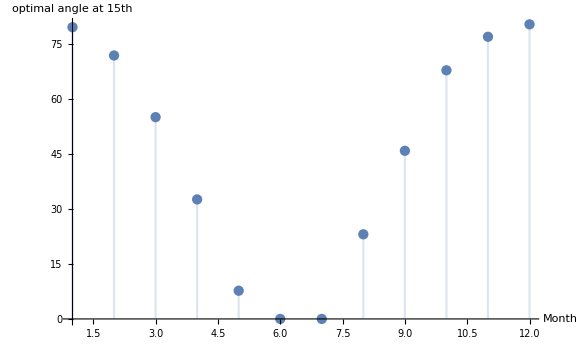
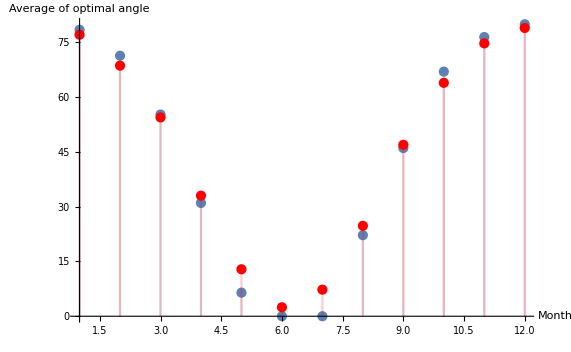
```mathematica
20/6 -Graphics-
september: -Graphics-
Every 15th day of the month: -Graphics-
18/7-Graphics3D-
20/6-Graphics3D-
20/12 -Graphics3D-
comparison with old 1-Cos[i] (red) -Graphics-
```

```mathematica
{{DateObject[{2016,1,1}],78.3614},{DateObject[{2016,1,2}],78.2744},{DateObject[{2016,1,3}],78.1784},{DateObject[{2016,1,4}],78.0734},{DateObject[{2016,1,5}],78.7095},{DateObject[{2016,1,6}],78.5912},{DateObject[{2016,1,7}],78.4385},{DateObject[{2016,1,8}],78.276},{DateObject[{2016,1,9}],78.1295},{DateObject[{2016,1,10}],77.9482},{DateObject[{2016,1,11}],77.7837},{DateObject[{2016,1,12}],77.6108},{DateObject[{2016,1,13}],77.4022},{DateObject[{2016,1,14}],77.2124},{DateObject[{2016,1,15}],77.0146},{DateObject[{2016,1,16}],76.8091},{DateObject[{2016,1,17}],76.5962},{DateObject[{2016,1,18}],76.3451},{DateObject[{2016,1,19}],76.1168},{DateObject[{2016,1,20}],75.8815},{DateObject[{2016,1,21}],75.6732},{DateObject[{2016,1,22}],75.4256},{DateObject[{2016,1,23}],75.1715},{DateObject[{2016,1,24}],74.9111},{DateObject[{2016,1,25}],74.6446},{DateObject[{2016,1,26}],74.4122},{DateObject[{2016,1,27}],74.1351},{DateObject[{2016,1,28}],73.8523},{DateObject[{2016,1,29}],73.6085},{DateObject[{2016,1,30}],73.3581},{DateObject[{2016,1,31}],73.1131},{DateObject[{2016,2,1}],72.8084},{DateObject[{2016,2,2}],72.5514},{DateObject[{2016,2,3}],72.2331},{DateObject[{2016,2,4}],71.9622},{DateObject[{2016,2,5}],71.6297},{DateObject[{2016,2,6}],71.3439},{DateObject[{2016,2,7}],71.05},{DateObject[{2016,2,8}],70.6958},{DateObject[{2016,2,9}],70.3866},{DateObject[{2016,2,10}],70.0695},{DateObject[{2016,2,11}],69.7451},{DateObject[{2016,2,12}],69.4136},{DateObject[{2016,2,13}],69.0246},{DateObject[{2016,2,14}],68.6802},{DateObject[{2016,2,15}],68.3302},{DateObject[{2016,2,16}],67.9751},{DateObject[{2016,2,17}],67.6154},{DateObject[{2016,2,18}],67.2517},{DateObject[{2016,2,19}],66.8845},{DateObject[{2016,2,20}],66.5144},{DateObject[{2016,2,21}],66.1416},{DateObject[{2016,2,22}],65.7667},{DateObject[{2016,2,23}],65.39},{DateObject[{2016,2,24}],65.0117},{DateObject[{2016,2,25}],64.6322},{DateObject[{2016,2,26}],64.2516},{DateObject[{2016,2,27}],63.9405},{DateObject[{2016,2,28}],63.56},{DateObject[{2016,2,29}],63.1785},{DateObject[{2016,3,1}],62.7955},{DateObject[{2016,3,2}],62.4094},{DateObject[{2016,3,3}],62.018},{DateObject[{2016,3,4}],61.6185},{DateObject[{2016,3,5}],61.2728},{DateObject[{2016,3,6}],60.8422},{DateObject[{2016,3,7}],60.3944},{DateObject[{2016,3,8}],59.9281},{DateObject[{2016,3,9}],59.4813},{DateObject[{2016,3,10}],58.9728},{DateObject[{2016,3,11}],58.448},{DateObject[{2016,3,12}],57.9086},{DateObject[{2016,3,13}],57.3788},{DateObject[{2016,3,14}],56.8152},{DateObject[{2016,3,15}],56.2441},{DateObject[{2016,3,16}],55.6673},{DateObject[{2016,3,17}],55.1082},{DateObject[{2016,3,18}],54.526},{DateObject[{2016,3,19}],53.9429},{DateObject[{2016,3,20}],53.3599},{DateObject[{2016,3,21}],51.4032},{DateObject[{2016,3,22}],52.2235},{DateObject[{2016,3,23}],51.6463},{DateObject[{2016,3,24}],51.0983},{DateObject[{2016,3,25}],50.5279},{DateObject[{2016,3,26}],49.9617},{DateObject[{2016,3,27}],49.398},{DateObject[{2016,3,28}],48.8466},{DateObject[{2016,3,29}],48.2526},{DateObject[{2016,3,30}],47.6269},{DateObject[{2016,3,31}],46.9281},{DateObject[{2016,4,1}],46.2106},{DateObject[{2016,4,2}],45.4661},{DateObject[{2016,4,3}],44.7083},{DateObject[{2016,4,4}],43.8993},{DateObject[{2016,4,5}],43.1687},{DateObject[{2016,4,6}],42.4665},{DateObject[{2016,4,7}],41.7975},{DateObject[{2016,4,8}],41.1657},{DateObject[{2016,4,9}],40.5775},{DateObject[{2016,4,10}],40.0194},{DateObject[{2016,4,11}],39.4883},{DateObject[{2016,4,12}],38.9811},{DateObject[{2016,4,13}],38.5415},{DateObject[{2016,4,14}],38.0787},{DateObject[{2016,4,15}],37.6309},{DateObject[{2016,4,16}],37.1881},{DateObject[{2016,4,17}],36.7293},{DateObject[{2016,4,18}],36.2288},{DateObject[{2016,4,19}],35.6653},{DateObject[{2016,4,20}],35.03},{DateObject[{2016,4,21}],34.2841},{DateObject[{2016,4,22}],33.5378},{DateObject[{2016,4,23}],32.7905},{DateObject[{2016,4,24}],25.5011},{DateObject[{2016,4,25}],26.5871},{DateObject[{2016,4,26}],27.6665},{DateObject[{2016,4,27}],28.7392},{DateObject[{2016,4,28}],29.6253},{DateObject[{2016,4,29}],29.1156},{DateObject[{2016,4,30}],28.655},{DateObject[{2016,5,1}],28.2333},{DateObject[{2016,5,2}],27.8457},{DateObject[{2016,5,3}],27.4809},{DateObject[{2016,5,4}],27.1134},{DateObject[{2016,5,5}],26.708},{DateObject[{2016,5,6}],26.2305},{DateObject[{2016,5,7}],25.6913},{DateObject[{2016,5,8}],25.067},{DateObject[{2016,5,9}],24.4372},{DateObject[{2016,5,10}],23.7472},{DateObject[{2016,5,11}],23.0813},{DateObject[{2016,5,12}],22.4955},{DateObject[{2016,5,13}],21.9342},{DateObject[{2016,5,14}],21.4389},{DateObject[{2016,5,15}],20.996},{DateObject[{2016,5,16}],20.5869},{DateObject[{2016,5,17}],20.2456},{DateObject[{2016,5,18}],19.908},{DateObject[{2016,5,19}],19.6462},{DateObject[{2016,5,20}],19.3599},{DateObject[{2016,5,21}],19.083},{DateObject[{2016,5,22}],18.8034},{DateObject[{2016,5,23}],18.5395},{DateObject[{2016,5,24}],18.2019},{DateObject[{2016,5,25}],17.8253},{DateObject[{2016,5,26}],17.4077},{DateObject[{2016,5,27}],16.955},{DateObject[{2016,5,28}],16.4815},{DateObject[{2016,5,29}],16.0064},{DateObject[{2016,5,30}],15.5485},{DateObject[{2016,5,31}],15.1215},{DateObject[{2016,6,1}],14.763},{DateObject[{2016,6,2}],14.4061},{DateObject[{2016,6,3}],14.0903},{DateObject[{2016,6,4}],13.8137},{DateObject[{2016,6,5}],13.5686},{DateObject[{2016,6,6}],13.3546},{DateObject[{2016,6,7}],13.1548},{DateObject[{2016,6,8}],12.9947},{DateObject[{2016,6,9}],12.8348},{DateObject[{2016,6,10}],12.6915},{DateObject[{2016,6,11}],12.5959},{DateObject[{2016,6,12}],12.4859},{DateObject[{2016,6,13}],12.3902},{DateObject[{2016,6,14}],12.3083},{DateObject[{2016,6,15}],12.2398},{DateObject[{2016,6,16}],12.1845},{DateObject[{2016,6,17}],12.1423},{DateObject[{2016,6,18}],12.1129},{DateObject[{2016,6,19}],12.0963},{DateObject[{2016,6,20}],12.0925},{DateObject[{2016,6,21}],12.1014},{DateObject[{2016,6,22}],12.1229},{DateObject[{2016,6,23}],12.1184},{DateObject[{2016,6,24}],12.1653},{DateObject[{2016,6,25}],12.2246},{DateObject[{2016,6,26}],12.2585},{DateObject[{2016,6,27}],12.3431},{DateObject[{2016,6,28}],12.404},{DateObject[{2016,6,29}],12.5144},{DateObject[{2016,6,30}],12.605},{DateObject[{2016,7,1}],12.7133},{DateObject[{2016,7,2}],12.8665},{DateObject[{2016,7,3}],13.011},{DateObject[{2016,7,4}],13.1779},{DateObject[{2016,7,5}],13.3693},{DateObject[{2016,7,6}],13.5873},{DateObject[{2016,7,7}],13.8343},{DateObject[{2016,7,8}],14.1126},{DateObject[{2016,7,9}],14.4246},{DateObject[{2016,7,10}],14.7719},{DateObject[{2016,7,11}],15.1548},{DateObject[{2016,7,12}],15.5711},{DateObject[{2016,7,13}],16.015},{DateObject[{2016,7,14}],16.4764},{DateObject[{2016,7,15}],16.9408},{DateObject[{2016,7,16}],17.3927},{DateObject[{2016,7,17}],17.8276},{DateObject[{2016,7,18}],18.2025},{DateObject[{2016,7,19}],18.5434},{DateObject[{2016,7,20}],18.815},{DateObject[{2016,7,21}],19.1002},{DateObject[{2016,7,22}],19.3802},{DateObject[{2016,7,23}],19.616},{DateObject[{2016,7,24}],19.9217},{DateObject[{2016,7,25}],20.2511},{DateObject[{2016,7,26}],20.5787},{DateObject[{2016,7,27}],20.974},{DateObject[{2016,7,28}],21.397},{DateObject[{2016,7,29}],21.8749},{DateObject[{2016,7,30}],22.4141},{DateObject[{2016,7,31}],22.9842},{DateObject[{2016,8,1}],23.6357},{DateObject[{2016,8,2}],24.2714},{DateObject[{2016,8,3}],24.9546},{DateObject[{2016,8,4}],25.5615},{DateObject[{2016,8,5}],26.1328},{DateObject[{2016,8,6}],26.6257},{DateObject[{2016,8,7}],27.0399},{DateObject[{2016,8,8}],27.443},{DateObject[{2016,8,9}],27.7904},{DateObject[{2016,8,10}],28.1509},{DateObject[{2016,8,11}],28.5755},{DateObject[{2016,8,12}],29.001},{DateObject[{2016,8,13}],29.4839},{DateObject[{2016,8,14}],29.1247},{DateObject[{2016,8,15}],28.3329},{DateObject[{2016,8,16}],27.0877},{DateObject[{2016,8,17}],25.8305},{DateObject[{2016,8,18}],32.494},{DateObject[{2016,8,19}],33.2434},{DateObject[{2016,8,20}],33.9532},{DateObject[{2016,8,21}],34.7007},{DateObject[{2016,8,22}],35.3898},{DateObject[{2016,8,23}],35.9939},{DateObject[{2016,8,24}],36.5289},{DateObject[{2016,8,25}],37.0281},{DateObject[{2016,8,26}],37.4536},{DateObject[{2016,8,27}],37.8643},{DateObject[{2016,8,28}],38.3345},{DateObject[{2016,8,29}],38.7725},{DateObject[{2016,8,30}],39.2731},{DateObject[{2016,8,31}],39.7551},{DateObject[{2016,9,1}],40.2691},{DateObject[{2016,9,2}],40.8342},{DateObject[{2016,9,3}],41.4182},{DateObject[{2016,9,4}],42.0377},{DateObject[{2016,9,5}],42.706},{DateObject[{2016,9,6}],43.4242},{DateObject[{2016,9,7}],44.1298},{DateObject[{2016,9,8}],44.9053},{DateObject[{2016,9,9}],45.6286},{DateObject[{2016,9,10}],46.3946},{DateObject[{2016,9,11}],47.1185},{DateObject[{2016,9,12}],47.769},{DateObject[{2016,9,13}],48.3931},{DateObject[{2016,9,14}],48.9816},{DateObject[{2016,9,15}],49.5355},{DateObject[{2016,9,16}],50.0761},{DateObject[{2016,9,17}],50.6428},{DateObject[{2016,9,18}],51.188},{DateObject[{2016,9,19}],51.7621},{DateObject[{2016,9,20}],52.3138},{DateObject[{2016,9,21}],51.2006},{DateObject[{2016,9,22}],53.449},{DateObject[{2016,9,23}],54.0068},{DateObject[{2016,9,24}],54.5886},{DateObject[{2016,9,25}],55.147},{DateObject[{2016,9,26}],55.7045},{DateObject[{2016,9,27}],56.2798},{DateObject[{2016,9,28}],56.8293},{DateObject[{2016,9,29}],57.371},{DateObject[{2016,9,30}],57.9257},{DateObject[{2016,10,1}],58.4446},{DateObject[{2016,10,2}],58.9769},{DateObject[{2016,10,3}],59.4629},{DateObject[{2016,10,4}],59.9262},{DateObject[{2016,10,5}],60.4136},{DateObject[{2016,10,6}],60.8352},{DateObject[{2016,10,7}],61.2333},{DateObject[{2016,10,8}],61.6778},{DateObject[{2016,10,9}],62.044},{DateObject[{2016,10,10}],62.3979},{DateObject[{2016,10,11}],62.8193},{DateObject[{2016,10,12}],63.1637},{DateObject[{2016,10,13}],63.5078},{DateObject[{2016,10,14}],63.9243},{DateObject[{2016,10,15}],64.2699},{DateObject[{2016,10,16}],64.6175},{DateObject[{2016,10,17}],64.9669},{DateObject[{2016,10,18}],65.3808},{DateObject[{2016,10,19}],65.731},{DateObject[{2016,10,20}],66.0821},{DateObject[{2016,10,21}],66.4336},{DateObject[{2016,10,22}],66.8412},{DateObject[{2016,10,23}],67.1903},{DateObject[{2016,10,24}],67.5383},{DateObject[{2016,10,25}],67.9371},{DateObject[{2016,10,26}],68.2797},{DateObject[{2016,10,27}],68.6193},{DateObject[{2016,10,28}],68.9553},{DateObject[{2016,10,29}],69.2869},{DateObject[{2016,10,30}],69.6645},{DateObject[{2016,10,31}],69.9859},{DateObject[{2016,11,1}],70.3018},{DateObject[{2016,11,2}],70.6116},{DateObject[{2016,11,3}],70.9677},{DateObject[{2016,11,4}],71.2655},{DateObject[{2016,11,5}],71.5569},{DateObject[{2016,11,6}],71.8421},{DateObject[{2016,11,7}],72.1756},{DateObject[{2016,11,8}],72.4493},{DateObject[{2016,11,9}],72.7175},{DateObject[{2016,11,10}],72.9807},{DateObject[{2016,11,11}],73.2929},{DateObject[{2016,11,12}],73.5468},{DateObject[{2016,11,13}],73.754},{DateObject[{2016,11,14}],74.0082},{DateObject[{2016,11,15}],74.3007},{DateObject[{2016,11,16}],74.5482},{DateObject[{2016,11,17}],74.7927},{DateObject[{2016,11,18}],75.0705},{DateObject[{2016,11,19}],75.3065},{DateObject[{2016,11,20}],75.5387},{DateObject[{2016,11,21}],75.7995},{DateObject[{2016,11,22}],76.0214},{DateObject[{2016,11,23}],76.2384},{DateObject[{2016,11,24}],76.4802},{DateObject[{2016,11,25}],76.6853},{DateObject[{2016,11,26}],76.913},{DateObject[{2016,11,27}],77.1051},{DateObject[{2016,11,28}],77.3179},{DateObject[{2016,11,29}],77.4959},{DateObject[{2016,11,30}],77.6929},{DateObject[{2016,12,1}],77.8558},{DateObject[{2016,12,2}],78.0363},{DateObject[{2016,12,3}],78.2081},{DateObject[{2016,12,4}],78.3462},{DateObject[{2016,12,5}],78.5003},{DateObject[{2016,12,6}],78.6453},{DateObject[{2016,12,7}],78.7808},{DateObject[{2016,12,8}],78.1288},{DateObject[{2016,12,9}],78.1961},{DateObject[{2016,12,10}],78.2866},{DateObject[{2016,12,11}],78.3686},{DateObject[{2016,12,12}],78.4419},{DateObject[{2016,12,13}],78.5065},{DateObject[{2016,12,14}],78.5905},{DateObject[{2016,12,15}],78.6368},{DateObject[{2016,12,16}],78.6741},{DateObject[{2016,12,17}],78.7023},{DateObject[{2016,12,18}],78.7215},{DateObject[{2016,12,19}],78.7581},{DateObject[{2016,12,20}],78.7584},{DateObject[{2016,12,21}],78.7761},{DateObject[{2016,12,22}],78.7574},{DateObject[{2016,12,23}],78.756},{DateObject[{2016,12,24}],78.7182},{DateObject[{2016,12,25}],78.6978},{DateObject[{2016,12,26}],78.6682},{DateObject[{2016,12,27}],78.6293},{DateObject[{2016,12,28}],78.5811},{DateObject[{2016,12,29}],78.495},{DateObject[{2016,12,30}],78.428}}
```